## Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"bouyancy.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"drag.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"visualizations.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Stability.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"COM.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"AVS.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"boats.m"}]]
```

```mathematica
boatboatboat[boat_]:=Quiet@Module[{doesFloat,doesFloatFlat, trimAngle,stabilityPlot,stabilityAngles},
doesFloat=Volume[region/.boat]Quantity[, ("Centimeters")^3]*Quantity[1, ("Grams")/("Centimeters")^3]>totalMass[boat]Quantity[, "Grams"];
doesFloatFlat=rightingArm[boat,{0,1,0},N@10 Degree]>0&&rightingArm[boat,{0,1,0},N@-10 Degree]<0;
trimAngle=Round[avs[boat,{1,0,0},0]*180/Pi] Quantity[, "AngularDegrees"];
stabilityPlot=Plot[rightingArm[boat,{0,1,0},θ],{θ,-Pi,Pi},PlotPoints->6, MaxRecursion->2];
stabilityAngles=DeleteDuplicates@Round[Table[avs[boat,{0,1,0},i],{i,-Pi,Pi,Pi/3}]*180/Pi] Quantity[, "AngularDegrees"];
bounds=Round[RegionBounds[region/.boat]/.{min_,max_}:>max-min,0.1]Quantity[, "Centimeters"];
floatHeight=boatWaterline[boat,{0,0,1}];
area=underwaterArea[boat,{0,0,1},floatHeight]Quantity[, ("Centimeters")^2];

Grid[{{Style[name/.boat,FontSize->60,FontFamily->"Purisa"],SpanFromLeft},
{showBoat[boat,{0,0,1}],SpanFromLeft},
{"Is it a boat?","Boatboat."},
{"How big is it?",bounds},
{"Does it float?",doesFloat},
{"How much is underwater?",area},
{"Stability curve",stabilityPlot},
{"Does it float flat?",doesFloatFlat},
{"Trim Angle?",trimAngle},
{"What's the AVS?",stabilityAngles}
},Frame->All]
]
```

111.769

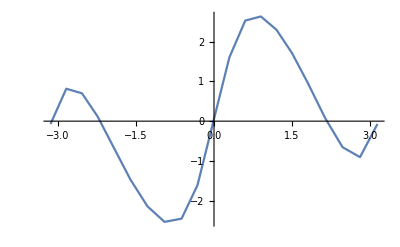
Crapboat | 
-Graphics3D- | 
Is it a boat? | Boatboat.
How big is it? | {9.5 cm,16.7 cm,3.3 cm}
Does it float? | True
How much is underwater? | 132.898 cm^2
Stability curve | -Graphics-
Does it float flat? | True
Trim Angle? | -51 °
What's the AVS? | {-180 °,-125 °,-1 °,124 °,180 °}

```mathematica
boatboatboat[boat]
```

915.743

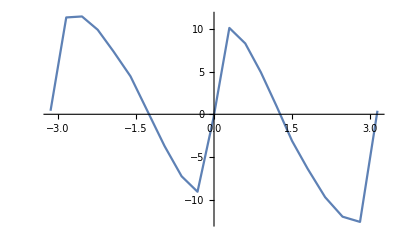
Bestboat | 
-Graphics3D- | 
Is it a boat? | Boatboat.
How big is it? | {49.3 cm,15. cm,50.9 cm}
Does it float? | True
How much is underwater? | 573.818 cm^2
Stability curve | -Graphics-
Does it float flat? | True
Trim Angle? | 0 °
What's the AVS? | {-180 °,-72 °,0 °,73 °,180 °}

```mathematica
boatboatboat[besterboat]
```